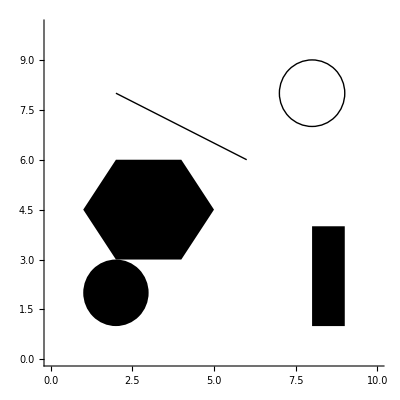

```mathematica
(*drawing rectangles*)

Graphics[{Disk[{2,2},1],
Circle[{8,8},1],
Rectangle[{8,1},{9,4}],
Line[{{2,8},{6,6}}],
Polygon[{{2,6},{1,4.5},{2,3},{4,3},{5,4.5},{4,6}}]
},
Axes->True,PlotRange->{{0,10},{0,10}}]
```

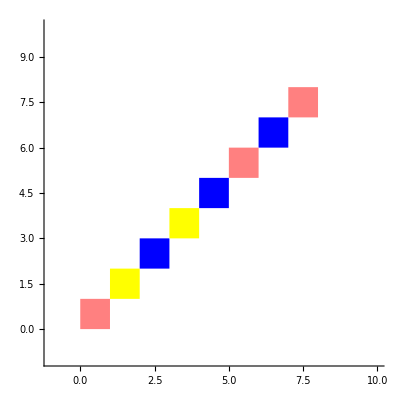

```mathematica
Graphics[
{
Pink,Rectangle[{0,0},{1,1}],
Yellow,Rectangle[{1,1},{2,2}],Blue,Rectangle[{2,2},{3,3}],Yellow,Rectangle[{3,3},{4,4}],Blue,Rectangle[{4,4},{5,5}],Pink,Rectangle[{5,5},{6,6}],
Blue,Rectangle[{6,6},{7,7}],Pink,Rectangle[{7,7},{8,8}],
},
Axes->True,PlotRange->{{-1,10},{-1,10}}
]
```

```mathematica
rec = Table[Rectangle[{a,a},{a+1,a+1}],{a,1,6,1}]
```

{Rectangle[{1,1},{2,2}],Rectangle[{2,2},{3,3}],Rectangle[{3,3},{4,4}],Rectangle[{4,4},{5,5}],Rectangle[{5,5},{6,6}],Rectangle[{6,6},{7,7}]}

```mathematica
rec
```

{Rectangle[{1,1},{2,2}],Rectangle[{2,2},{3,3}],Rectangle[{3,3},{4,4}],Rectangle[{4,4},{5,5}],Rectangle[{5,5},{6,6}],Rectangle[{6,6},{7,7}]}

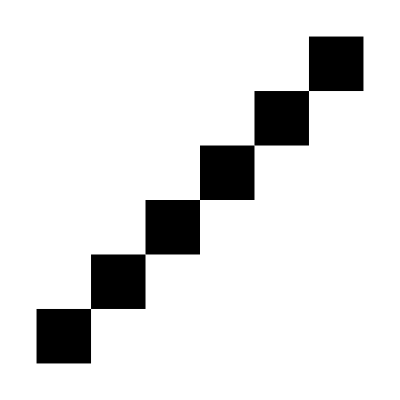

```mathematica
Graphics[rec]
```

```mathematica
Manipulate[
Graphics[
{Table[{RGBColor[RandomReal[],RandomReal[],RandomReal[]],Rectangle[{a,a},{a+1,a+1}],
Disk[{a+n,a+m}]},{a,1,6,1}]
},PlotRange->{{-1,10},{-1,10}}
],{n,0,1},{m,0,1}
]
```

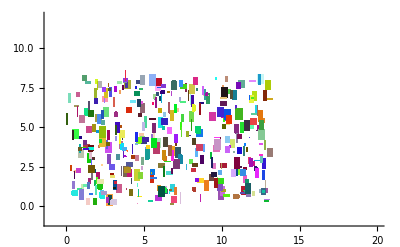

```mathematica
Graphics[
Table[
{RGBColor[RandomReal[],RandomReal[],RandomReal[]],
Rectangle[{x=RandomReal[13],y=RandomReal[8]},{x+RandomReal[0.4],y+RandomReal[0.7]}]
},{i,1,400}
],Axes->True,PlotRange->{{-1,20},{-1,12}}
]
```

```mathematica
Manipulate[
ListPlot[
Table[{RandomReal[1],RandomReal[1]},{i,1,a}]
],{a,10,1000,1}
]
```